```mathematica
(* https://www.expii.com/solve/46/5 *)
(* You are living in the post-apocalyptic wasteland that used to be the United States, and there is a zombie outbreak. You are surrounded,by N zombies equally spaced around a circle of radius 200 meters in an open field. While making your escape plan you note several things: they are slow, they can only travel at one tenth of your speed, they are stupid, with rotting brains they can only move directly at your current position, they can not anticipate your moves, and they can not cooperate with one another. If any zombie gets within 1 meter of you, you will be caught. What is the maximum value of N for which you have a strategy to escape from them? *)

(* Best strategy is moving in a line, for example vertically *)
(* In that case the closest zombie would be the one closest to the y-axis: *)
Clear[y,x0,y0];
n=362;
x0=N[200*Sin[Pi/n]]
y0=N[200*Cos[Pi/n]]
(* The equation of motion of the zombie is given by the following two equations: *)
(* 1 = (vx^2+vy^2)^(1/2) which results in dt/dx = - Sqrt[1+y'[x]^2] *)
(* y'[x] = y/(x-10 t) *)
(* Combining them results in  *)
DSolve[{x y''[x] - 10 Sqrt[1+y'[x]^2]==0,y[x0]==y0, y'[x0]==y0/x0},y[x],x]
```

1.73566

199.992

{{y[x]→181.811+0.0598136/x^9+0.0422187 x^11}}

```mathematica
y[x_]=y[x]/.%[[1]]
```

181.811+0.0598136/x^9+0.0422187 x^11

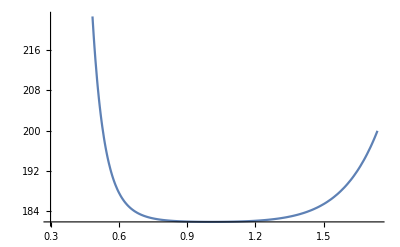

```mathematica
Plot[y[x],{x,0.3,x0}]
```

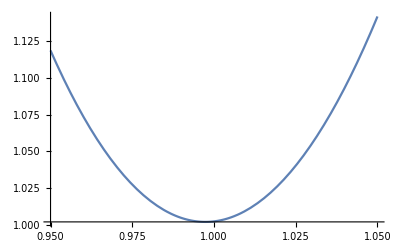

```mathematica
(* Distance between zombie and me: *)
t[xx_]:=NIntegrate[Sqrt[1+y'[x]^2],{x,xx,x0}];
Plot[Sqrt[xx^2+(10 t[xx]-y[xx])^2],{xx,1.05,0.95}]
```